Importing your calibration films and Creating the dose calibration curves

Retrieve the file paths of the calibration files and then import the images.

```mathematica
Clear["Global`*"]
```

```mathematica
calFilePath=SystemDialogInput["FileOpen"]
```

/Users/cptfinch/Documents/maths/gafchromic/my cal and uniformity films/img001.tif

```mathematica
calFile=Import[calFilePath]
```

-Graphics-

The next step is to obtain the rectangular regions of interest from the imported images and to obtain a list of the regions in order of increasing dose. Incidentally for best practice the calibration strips should be scanned during one scan; in other words all of the calibration strips should be placed on the scanner bed and scanned together. This removes any variation in the scanner response over successive scans - removing the variability in response caused by inter-scan variability.   

To select the regions of interest use the following steps: Make the image below active by clicking on it; a number of options will appear along the bottom of image, select the rectangular select tool; drag over the irradiated regions in order to create selected central rectangular regions of the irradiated parts of each strip. 

Once all regions are selected, copy and paste the list to the right of calRoiList=

/Users/cptfinch/Documents/maths/gafchromic/my cal and uniformity films/img001.tif[First]

```mathematica
calRoiList={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} ;
```

The following ColorSeparate function returns an n by 4 matrix instead of an n by 3 matrix. In other words there are four columns where I would have expected three columns, three since that corresponds to the three colour channels. The fourth column seems to be simply blank, so I am not sure where it comes from.

```mathematica
rgbCalList=Map[ColorSeparate,calRoiList];
```

Obtain here lists containing the calibration regions for respective colour channels. They are obtained by extracting them from the rgbCalList.

```mathematica
redCalRois=rgbCalList[[All,1]];
```

```mathematica
greenCalRois=rgbCalList[[All,2]];
```

```mathematica
blueCalRois=rgbCalList[[All,3]];
```

A pure function f to obtain the mean value of a calibration region.

```mathematica
f[x_]:=Mean[Flatten[ImageData[x]]];
```

f is mapped over each calibration region to obtain a list of values corresponding to the mean pixel values of the calibration regions. Pixel values are normalized to 1. i.e. 0..65535 is mapped to 0..1

```mathematica
redCal=Map[f,redCalRois];
```

```mathematica
blueCal=Map[f,blueCalRois];
```

```mathematica
greenCal=Map[f,greenCalRois];
```

Sort the values in order corresonding from high pixel value to low pixel value. This corresponds to the order of low dose to high dose.

```mathematica
redCalPixelValueLowToHighDose=Sort[redCal,Greater];
```

```mathematica
blueCalPixelValueLowToHighDose=Sort[blueCal,Greater];
```

```mathematica
greenCalPixelValueLowToHighDose=Sort[greenCal,Greater];
```

Input the doses given to the calibration strips in the order low to high dose. Here I have specified dose in Gy. Be sure to keep it in this format - each number separated by a comma and curly braces at each end.

```mathematica
cal1Doses={0,1/2,1,2,4,7,9};
```

```mathematica
redCalPoints=Transpose[{cal1Doses,redCalPixelValueLowToHighDose}];
blueCalPoints=Transpose[{cal1Doses,blueCalPixelValueLowToHighDose}];
greenCalPoints=Transpose[{cal1Doses,greenCalPixelValueLowToHighDose}];
```

```mathematica
redLine=FindFit[redCalPoints,(r+s*D)/(t+D),{r,s,t},D];
blueLine=FindFit[blueCalPoints,(r+s*D)/(t+D),{r,s,t},D];
greenLine=FindFit[greenCalPoints,(r+s*D)/(t+D),{r,s,t},D];
```

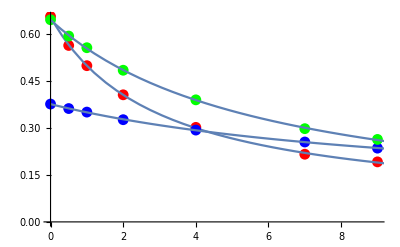

```mathematica
Show[ListPlot[redCalPoints, PlotStyle->Red],Plot[{(r+s*D)/(t+D)/.redLine}, {D, 0, 15}],
	ListPlot[blueCalPoints, PlotStyle->Blue], Plot[{(r+s*D)/(t+D)/.blueLine}, {D, 0, 15}],
	ListPlot[greenCalPoints, PlotStyle->Green],Plot[{(r+s*D)/(t+D)/.greenLine}, {D, 0, 15}]]
```

## Converting Application films to dose using the Multi-channel method

```mathematica
appFilmFilePath=SystemDialogInput["FileOpen"];
appFilm=Import[appFilmFilePath];
```

```mathematica
redChannel=ColorSeparate[appFilm,"R"];
blueChannel=ColorSeparate[appFilm,"G"];
greenChannel=ColorSeparate[appFilm,"B"];
```

```mathematica
redFit[dose_]=((r+s*dose)/(t+dose))/.redLine;
blueFit[dose_]=((r+s*dose)/(t+dose))/.blueLine;
greenFit[dose_]=((r+s*dose)/(t+dose))/.greenLine;
```

```mathematica
f[pixelR_,pixelB_,pixelG_]:=bestDose/.Last[Minimize[(pixelR-redFit[bestDose])^2+(pixelB-blueFit[bestDose])^2+(pixelG-greenFit[bestDose])^2,bestDose]];
```

```mathematica
ImageApply[f,{redChannel,blueChannel,greenChannel}]
```

The following is test data

```mathematica
redPixel1 = ImageData[redChannel][[1, 1]]

bluePixel1 = ImageData[blueChannel][[1, 1]]

greenPixel1 = ImageData[greenChannel][[1, 1]]
```

```mathematica
croppedApp=ImageCrop[appFilm,{2,2}]
```

-Graphics-

```mathematica
croppedFilm[_width,_height]:=ImageCrop[appFilm,{width,height}]
```

```mathematica
smallerFilm=ImageCrop[appFilm, {2,2}]
Map[l,ImageData[smallerFilm,{2}]]
```

-Graphics-

ImageData::imgprop: {2} is not a valid property for an image.

Part::partd: Part specification (GraphicsBox[TagBox[RasterBox[RawArray[ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NMinimize::nnum: The function value (-0.8955535312926842` + (GraphicsBox[TagBox[RasterBox[RawArray[ is not a number at {bestDose} = {-0.829053}.

General::stop: Further output of NMinimize :: nnum will be suppressed during this calculation.

ReplaceAll::reps: {bestDose} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {2} does not exist.

Part::partw: Part 3 of {2} does not exist.

ReplaceAll::reps: {bestDose} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ImageData::imginv: Expecting an image or graphics instead of bestDose/. bestDose.

ImageData[bestDose/.bestDose,bestDose/.bestDose]

```mathematica
croppedFilm[2,2]
```

croppedFilm[2,2]

```mathematica
blahd[_yep]:=yep*2
```

```mathematica
blahd[4]
```

blahd[4]

```mathematica
ImageCrop[appFilm,{2,2}]
```

-Graphics-

```mathematica
l[pixel_]:=bestDose/.Last[Minimize[(pixel[[1]]-redFit[bestDose])^2+(pixel[[2]]-blueFit[bestDose])^2+(pixel[[3]]-greenFit[bestDose])^2,bestDose]];
```

```mathematica
ImageApply[l,-Graphics-]
```

```mathematica
l[pixel_]:=bestDose/.Last[Minimize[(pixel[[1]]-redFit[bestDose])^2+(pixel[[2]]-blueFit[bestDose])^2+(pixel[[3]]-greenFit[bestDose])^2,bestDose<5 &&bestDose>2,bestDose]];
```

```mathematica
ImageData[%207]
```

-Graphics-

```mathematica
ImageData[%156]
```

{{{0.371069,0.447761,0.310719},{0.368612,0.447364,0.310491}},{{0.370809,0.448905,0.311192},{0.368566,0.448508,0.311604}}}

```mathematica
Last[{4,3,2}]
```

```mathematica
l[{0.3710688944838636,0.4477607385366598,0.31071946288242924}]
```

3.38007

```mathematica
ImageApply[#*6&,croppedApp]
```

-Graphics-

```mathematica
Map[func,ImageData[croppedApp]]
```

```mathematica
{func[{{0.3710688944838636,0.4477607385366598,0.31071946288242924},{0.3686121919584955,0.4473640039673457,0.3104905775539788}}],func[{{0.37080949111161976,0.44890516517891205,0.31119249256122683},{0.3685664148928054,0.44850843060959794,0.31160448615243763}}]}
Map[func,ImageData[croppedApp],{2}]
```

{func[{{0.371069,0.447761,0.310719},{0.368612,0.447364,0.310491}}],func[{{0.370809,0.448905,0.311192},{0.368566,0.448508,0.311604}}]}

{{func[{0.371069,0.447761,0.310719}],func[{0.368612,0.447364,0.310491}]},{func[{0.370809,0.448905,0.311192}],func[{0.368566,0.448508,0.311604}]}}

```mathematica
croppedFilm[2,2]
```

croppedFilm[2,2]

```mathematica
Map[l,ImageData[croppedFilm[2,2]],{2}]
```

ImageData::imginv: Expecting an image or graphics instead of croppedFilm[2, 2].

Part::partd: Part specification 2 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 2 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification 2 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NMinimize::nnum: The function value (-0.895554 + 2 ⟦ 1 ⟧)^2 + (-0.401758 + 2 ⟦ 2 ⟧)^2 + (-0.747834 + 2 ⟦ 3 ⟧)^2 is not a number at {bestDose} = {-0.829053}.

General::stop: Further output of NMinimize :: nnum will be suppressed during this calculation.

ReplaceAll::reps: {bestDose} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ImageData::imginv: Expecting an image or graphics instead of croppedFilm[bestDose/. bestDose, bestDose/. bestDose].

ImageData[croppedFilm[bestDose/.bestDose,bestDose/.bestDose]]

```mathematica
Map[l,ImageData[appFilm],{2}]
```

$Aborted

```mathematica
Map[l,ImageData[croppedApp],{2}]
```

```mathematica
{{3.3800694075890885,3.410693701660224},{3.373477673023367,3.395045616008423}}
```

```mathematica
ImageData[%213]
```

{{{1.,1.,1.},{1.,1.,1.}},{{1.,1.,1.},{1.,1.,1.}}}

```mathematica
Minimize
```

```mathematica
{1,2,3}[[2]]
```

2

```mathematica
ImageApply[f,-Graphics-]
```

ImageApply::bdf: Applying f to {0.371069, 0.447761, 0.310719} does not yield a number or list of numbers.

ImageApply[f,-Graphics-]

```mathematica
ImageApply[f,{croppedRed,croppedBlue,croppedGreen}]
```

```mathematica
croppedRed
```

-Graphics-

```mathematica
g[pixelR_,pixelB_,pixelG_]:=bestDose/.Last[Minimize[(pixelR-redFit[bestDose])^2+(pixelB-blueFit[bestDose])^2+(pixelG-greenFit[bestDose])^2,bestDose]]
```

```mathematica
blahd[fir_,sec_,thi_]=(fir+sec+thi)/3
```

```mathematica
g[0.5,0.5,0.5]
```

1.01878

```mathematica
ImageApply[g,{croppedRed,croppedBlue,croppedGreen}]
```

ImageApply::bdf: Applying g to {0.371069, 0.447761, 0.310719} does not yield a number or list of numbers.

```mathematica
ImageApply[g,{-Graphics-,-Graphics-,-Graphics-}]//ImageAdjust
```

```mathematica
ImageData[-Graphics-]
```

{{0.,0.},{0.,0.}}

```mathematica
-Graphics-
ImageData[-Graphics-]
```

-Graphics-

{{0.376516,0.375494},{0.376974,0.376226}}

```mathematica
ImageApply[g,-Graphics-]
```

ImageApply::bdf: Applying g to 0.371069 does not yield a number or list of numbers.

```mathematica
ImageApply[g,-Graphics-]
```

ImageApply::bdf: Applying g to 0.371069 does not yield a number or list of numbers.

```mathematica
ImageApply[g,-Graphics-,-Graphics-,-Graphics-]
```

ImageApply::nonopt: Options expected (instead of ) beyond position 2 in g, GraphicsBox[TagBox[RasterBox[RawArray[. An option must be a rule or a list of rules.

```mathematica
ImageApply[g,{-Graphics-,-Graphics-,-Graphics-}]
```

```mathematica
ImageData[-Graphics-]
```

{{0.376516,0.375494},{0.376974,0.376226}}

```mathematica
ImageApply[g,{-Graphics-,-Graphics-,-Graphics-}]
```

```mathematica
ImageApply[g,{Image[{{0.5,0.8},{0.5,0.5}}],Image[{{0.5,0.1},{0.5,0.5}}],Image[{{0.5,0.3},{0.5,0.5}}]}]
```

```mathematica
ImageData[-Graphics-]
```

{{1.01878,0.407006},{1.01878,1.01878}}

```mathematica
ImageApply[g,{-Graphics-,-Graphics-,-Graphics-}]
```

```mathematica
ImageApply
```

```mathematica
ImageData[-Graphics-]
```

{{1.,1.},{1.,1.}}



```mathematica
ArrayPlot[{{1.,1.},{1.,1.}}]
```

```mathematica
ImageApply[bestDose/.Last[Minimize[(#1-redFit[bestDose])^2+(#2-blueFit[bestDose])^2+(#3-greenFit[bestDose])^2,bestDose]&],croppedRed,croppedBlue,croppedGreen]
```

NMinimize::nnum: The function value (-0.895554 + #1)^2 + (-0.401758 + #2)^2 + (-0.747834 + #3)^2 is not a number at {bestDose} = {-0.829053}.

General::stop: Further output of NMinimize :: nnum will be suppressed during this calculation.

ReplaceAll::reps: {Minimize[(-1.93515  + Times[« 2 »]/Plus[« 2 »] + #1)^2 + (-3.99831  + Times[« 2 »]/Plus[« 2 »] + #2)^2 + (-3.84505  + Times[« 2 »]/Plus[« 2 »] + #3)^2, bestDose]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ImageApply::nonopt: Options expected (instead of ) beyond position 2 in bestDose/. Minimize[(-Plus[« 2 »] Power[« 2 »] + #1)^2 + (-Plus[« 2 »] Power[« 2 »] + #2)^2 + (-Plus[« 2 »] Power[« 2 »] + #3)^2, bestDose], GraphicsBox[TagBox[RasterBox[RawArray[. An option must be a rule or a list of rules.

ImageApply[bestDose/.Minimize[(-(1.93515+0.0366878 bestDose)/(2.95594+bestDose)+#1)^2+(-(3.99831+0.0703032 bestDose)/(10.636+bestDose)+#2)^2+(-(3.84505+0.00711172 bestDose)/(5.96275+bestDose)+#3)^2,bestDose],-Graphics-,-Graphics-,-Graphics-]

```mathematica
ImageData[croppedRed]
```

{{0.371069,0.368612},{0.370809,0.368566}}

```mathematica
redPixelbla = ImageData[redChannel]
Dimensions[redPixelbla]
```

```mathematica
{685,544}
ImageAssemble
```

```mathematica
f[redPixel1,bluePixel1,greenPixel1]
```

3.88121

```mathematica
croppedRed=ImageCrop[redChannel,{2,2}]
croppedBlue=ImageCrop[blueChannel,{2,2}]
croppedGreen=ImageCrop[greenChannel,{2,2}]

ImageData[croppedGreen][[1,1]]

MapThread[f,{croppedRed,croppedBlue,croppedGreen}]

ImageData[croppedRed]
```

0.310719

MapThread::mptd: Object  at position {2, 1} in f, {GraphicsBox[TagBox[RasterBox[RawArray[ has only 0 of required 1 dimensions.

MapThread[f,{-Graphics-,-Graphics-,-Graphics-}]

{{0.371069,0.368612},{0.370809,0.368566}}

```mathematica
wat=ImageApply[f,{croppedRed,croppedBlue,croppedGreen}]
```

```mathematica
ImageApply
```

```mathematica
ImageAdjust[wat]
```

-Graphics-

```mathematica
ImageHistogram[-Graphics-]
```

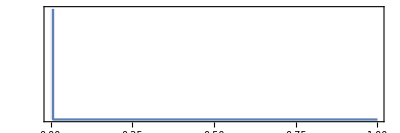
```mathematica
-Graphics-
ImageData[wat]
```

-Graphics-

{{1.,1.},{1.,1.}}